Units

```mathematica
μs=10^-6;
MHz=10^6;
PS=222 MHz;
PP=37 MHz;
Γ=100 MHz;
```

```mathematica
1/(√1.01-√(.01))(√1.01-√(((t-w/2)/(w/2))^2+0.01))/.t->w
```

0.

```mathematica
√1.01-√(.01)
```

0.904988

```mathematica
√1.01
```

1.00499

Laser Pulses

```mathematica
(* pulses describe the two laser pulses sent to the molecule. The list is in order of {Subscript[Ω, Stokes], Subscript[Ω, Pump], Subscript[Δ, Stokes], Subscript[Δ, Pump]}, where the former two are the time-dependent Rabi frequencies (proportional to intensities), and the latter two are the time-dependent single-photon detunings. For all pulses, PS and PP are the Rabi amplitudes, and DS and DP are the single-photon detuning amplitudes.*)
pulse1={Piecewise[{{PS, 0<t<w}}],Piecewise[{{PP, t1<t<t1+w}}],Piecewise[{{DS*(t-w/2)/w, 0<t<w}}],Piecewise[{{DP*(t-t1-w/2)/w, t1<t<t1+w}}]};
pulse2={Piecewise[{{PS/(√1.3-√(.3))(√1.3-√(((t-w/2)/(w/2))^2+0.3)), 0<t<w}}],Piecewise[{{PP/(√1.3-√(.3))(√1.3-√(((t-t1-w/2)/(w/2))^2+0.3)), t1<t<t1+w}}],Piecewise[{{DS*(t-w/2)/w, 0<t<w}}],Piecewise[{{DP*(t-t1-w/2)/w, t1<t<t1+w}}]};
```

```mathematica
laserPlot[pulse_,w0_,t10_,DS0_,DP0_]:=Plot[Evaluate[pulse/.{w->w0,t1->t10,DS->DS0,DP->DP0}],{t,0,30 μs},ImageSize->500,AspectRatio->1,Exclusions->None,PlotLegends->{"Ωs","Ωp","Δs","Δp"}]
```

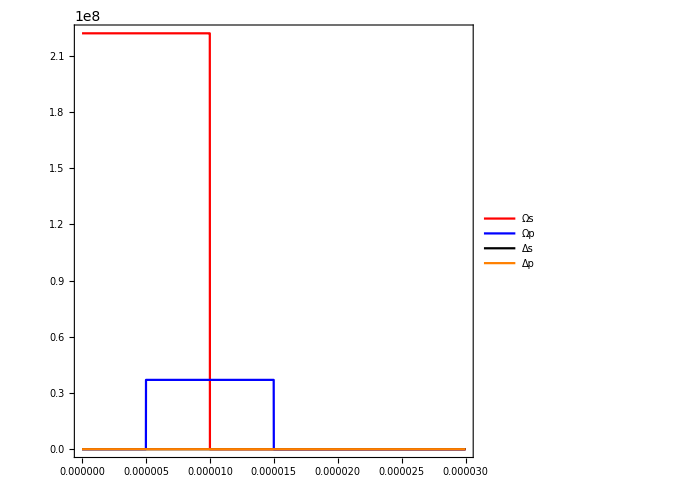
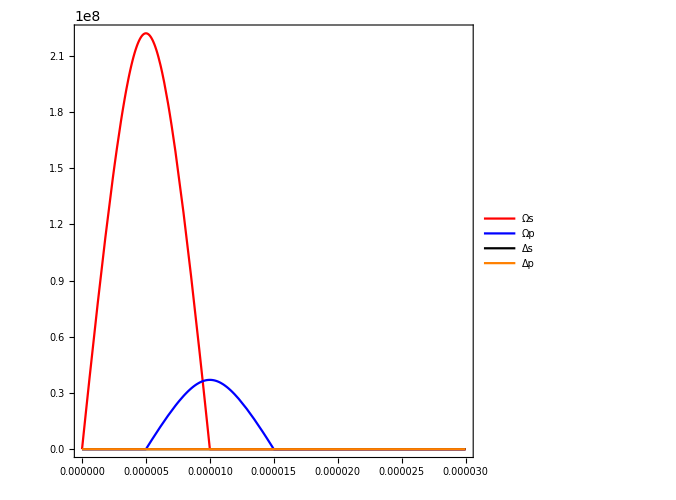

```mathematica
{laserPlot[pulse1,10μs,5μs,0,0],laserPlot[pulse2,10μs,5μs,0,0]}
```

```mathematica
H[Ωs_,Ωp_,Δs_,Δp_]:=2π({{0, 1/2 0.1897/0.1897 Ωp, 1/2(1.7432+0.67256)/0.1897 Ωp, 0}, {1/2 Ωp, Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2(1.7432+0.67256)/0.1897 Ωp, 0, Δp+(133.86-130.41)10^9-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, Δp-Δs}});
H1=H@@pulse1;
H2=H@@pulse2;
```

```mathematica
Eigensystem[H[8μs]/.{w->9μs,t1->6μs,DS->0,DP->0}][[2]]//Re
```

{{0.0678032,0.000362275,0.997698,0.0000115972},{-0.129475,0.70618,0.00858382,-0.677985},{0.0998906,0.707644,-0.0070341,0.681569},{0.983405,0.0234077,-0.0668384,-0.166684}}

```mathematica
P[t_]={p1[t],p2[t],p3[t],p4[t]};
init=P[0]=={1,0,0,0};
SE=ⅈ P'[t]==H[t].P[t];
```

AC Stark Shift

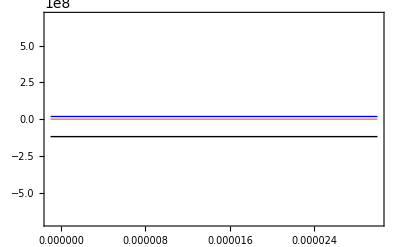

```mathematica
Plot[Evaluate@(Eigensystem[H1/.{t->9μs,w->9μs,t1->6μs,DS->0,DP->0}][[1]]//Re),{t,-1μs,30μs},PlotRange->{-0.7 10^9,0.7 10^9},Exclusions->None]
```

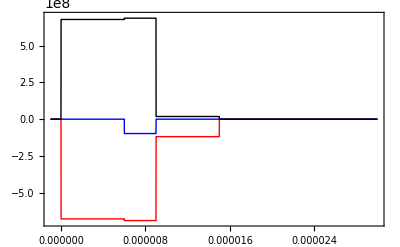

```mathematica
evals[t_,w0_,t10_,DS0_,DP0_]:=Re[Eigenvalues[H[t]/.{w->w0,t1->t10,DS->DS0,DP->DP0}]]
Plot[Evaluate@evals[t,9μs,6μs,0,0],{t,-1μs,30μs},PlotRange->{-0.7 10^9,0.7 10^9},Exclusions->None]
```

```mathematica
Evaluate@evals[-1μs,9μs,6μs,0,0]
```

{2.1677×10^10,0.,0.,0.}

Numerical solution

```mathematica
PSoln=ParametricNDSolve[{SE,init},{p1,p2,p3,p4},{t,0,40 μs},{w,t1,DS,DP},PrecisionGoal->9];
plots[w_,t1_,DS_,DP_]:={Plot[{Evaluate[Abs[p1[w,t1,DS,DP][t]]^2/.PSoln],Evaluate[ Abs[p4[w,t1,DS,DP][t]]^2/.PSoln]},{t,0 μs,20μs},ImageSize->500,AspectRatio->1,PlotLegends->{"p1","p4"},FrameLabel->{"t [s]",Abs[ψ]^2},PlotRange->All],laserPlot[w,t1,DS,DP]}
```

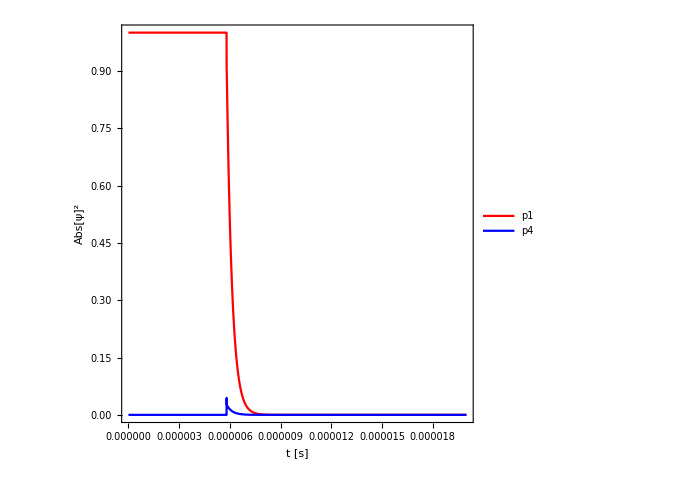
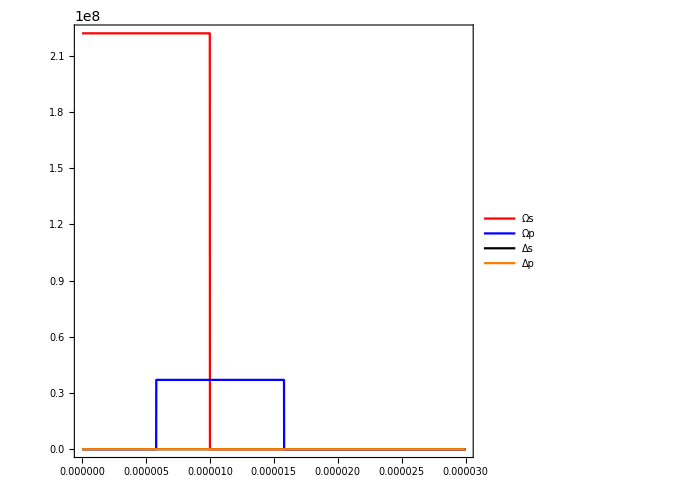

```mathematica
plots[10 μs,5.8 μs,0 MHz,0MHz]
```

```mathematica
Abs[p4[10 μs,9.95 μs,0 MHz,0MHz][11 μs]]^2/.PSoln
```

0.0234498

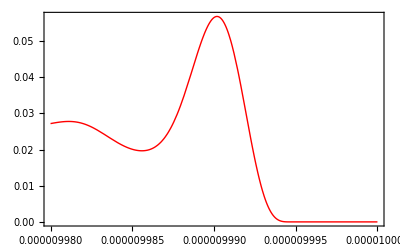

```mathematica
Plot[Evaluate[Abs[p4[10 μs,w,0 MHz,0MHz][11 μs]]^2/.PSoln],{w,9.98 μs,10μs}]
```

```mathematica
(*ContourPlot[Evaluate[Abs[p3[w,t1,222 MHz,37 MHz,0 MHz,0MHz][20 10^-6]]^2/. PSoln] ,{w,7 μs,9 μs},{t1,6 μs,8 μs},PlotLegends->Automatic,Axes -> True,Frame->False,Exclusions->None,AxesLabel->{"w","t1"}, PerformanceGoal->"Speed", Contours->20]*)
```

```mathematica
NMaximize[Evaluate[Abs[p4[10 μs,w,0 MHz,0MHz][11 μs]]^2/.PSoln],{w,9.5,9.9}]
```

{0.,{w→5.80267}}

```mathematica
p4test=p4[10 μs,w,0 MHz,0MHz]/.PSoln
```

ParametricFunction[<>][1/100000,w,0,0]

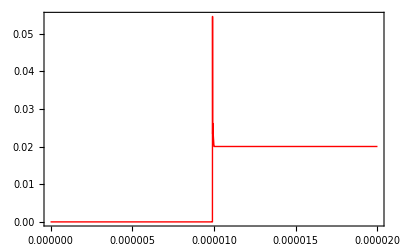

```mathematica
Plot[Abs[p4test[t]]^2,{t,0,20μs}]
```

```mathematica
H[t_]=2π({{0, 1/2 0.1897/0.1897 Ωp, 1/2(1.7432+0.67256)/0.1897 Ωp, 0}, {1/2 Ωp, Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2(1.7432+0.67256)/0.1897 Ωp, 0, Δp+(133.86-130.41)10^9-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, Δp-Δs}});
```

```mathematica
Re[Eigenvalues[H[30 μs]/.{t1->10μs,w-> 9μs,DS->0, DP->0}]]
```

{2.1677×10^10,0.,0.,0.}

```mathematica
H4=({{0, 1/2 0.1897/0.1897 Ωp, 1/2(1.7432+0.67256)/0.1897 Ωp, 0}, {1/2 Ωp, Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2(1.7432+0.67256)/0.1897 Ωp, 0, Δp+(133.86-130.41)10^9-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, Δp-Δs}});
```

H4

```mathematica
ev=Re[Eigenvalues[({{0, Ω1, 12.73 Ω1}, {Ω1, 0, 0}, {12.73 Ω1, 0, Δ}}),Cubics->True]]
```

{Re[0.333333 Δ+((0.209987-0.363708 ⅈ) (-1. Δ^2-489.159 Ω1^2))/((2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3))-(0.132283+0.229122 ⅈ) (2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3)],Re[0.333333 Δ+((0.209987+0.363708 ⅈ) (-1. Δ^2-489.159 Ω1^2))/((2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3))-(0.132283-0.229122 ⅈ) (2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3)],Re[0.333333 Δ-(0.419974 (-1. Δ^2-489.159 Ω1^2))/((2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3))+0.264567 (2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3)]}

```mathematica
FullSimplify[ev-(ev/.Ω1->0),Δ∈Reals]
```

{Re[(0.166667+0.288675 ⅈ) (Δ^3)^(1/3)+((0.166667-0.288675 ⅈ) (Δ^3)^(2/3))/Δ]+Re[((0.209987-0.363708 ⅈ) (-1. Δ^2-489.159 Ω1^2))/((2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3))-(0.132283+0.229122 ⅈ) (2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3)],Re[(0.166667-0.288675 ⅈ) (Δ^3)^(1/3)+((0.166667+0.288675 ⅈ) (Δ^3)^(2/3))/Δ]+Re[((0.209987+0.363708 ⅈ) (-1. Δ^2-489.159 Ω1^2))/((2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3))-(0.132283-0.229122 ⅈ) (2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3)],-Re[0.333333 (Δ^3)^(1/3)+(0.333333 (Δ^3)^(2/3))/Δ]+Re[(0.419974 Δ^2+205.434 Ω1^2+0.264567 (2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(2/3))/(2. Δ^3+1440.48 Δ Ω1^2+√(-108. Δ^4 Ω1^2-796343. Δ^2 Ω1^4-4.68176×10^8 Ω1^6))^(1/3)]}